Theoretical Constants

```mathematica
s2w:=0.23868;
Z:=6;Nn:=6;
Qw:=Z*(1.0-4*s2w)-Nn;
gev2fm=5.067730759;
Gf=1.1663787*10^-5/gev2fm^2;
alpha=1/137.035999139;
m=0.5109989461*10^(-3);
```

Experimental parameters

```mathematica
AW=12;
M=0.9314940954*AW;
e1=0.155;
e2[angl_]:=e1/(1+2e1/M*Sin[angl/2]^2);
q[angl_]:=Sqrt[4e1 e2[angl] Sin[angl/2]^2]*gev2fm;
Rch0:=2.46932;
Rcht0:=2.77098;
Rchtt0:=3.05006;
```

Experimental q (in fm^-1)

```mathematica
q1:=q[29/180Pi]
q2:=q[145/180Pi]
q3:=q[125/180Pi]
q1
q2
q3
```

0.393005

1.47974

1.37853

Forward measurement

Determination of the uncertaintly band based on nuclear models data

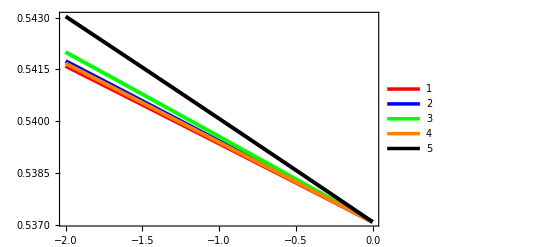

```mathematica
SetDirectory[NotebookDirectory[]];
anglesize=18;
file1="nuclmodel_001+.dat";
file2="nuclmodel_001-.dat";
file3="nuclmodel_002+.dat";
file4="nuclmodel_002-.dat";
file5="nuclmodel_003+.dat";
file6="nuclmodel_003-.dat";
file7="nuclmodel_004+.dat";
file8="nuclmodel_004-.dat";
file9="nuclmodel_005+.dat";
file10="nuclmodel_005-.dat";

filelength1=Length@Import[file1,"Lines"];
n1=filelength1;
filelength2=Length@Import[file3,"Lines"];
n2=filelength2;
filelength3=Length@Import[file5,"Lines"];
n3=filelength3;
filelength4=Length@Import[file7,"Lines"];
n4=filelength4;
filelength5=Length@Import[file9,"Lines"];
n5=filelength5;

xs1=OpenRead[file1];
data1=ReadList[xs1,{Number,Number,Number,Number},n1];
xs2=OpenRead[file2];
data2=ReadList[xs2,{Number,Number,Number,Number},n1];
xs3=OpenRead[file3];
data3=ReadList[xs3,{Number,Number,Number,Number},n2];
xs4=OpenRead[file4];
data4=ReadList[xs4,{Number,Number,Number,Number},n2];
xs5=OpenRead[file5];
data5=ReadList[xs5,{Number,Number,Number,Number},n3];
xs6=OpenRead[file6];
data6=ReadList[xs6,{Number,Number,Number,Number},n3];
xs7=OpenRead[file7];
data7=ReadList[xs7,{Number,Number,Number,Number},n4];
xs8=OpenRead[file8];
data8=ReadList[xs8,{Number,Number,Number,Number},n4];
xs9=OpenRead[file9];
data9=ReadList[xs9,{Number,Number,Number,Number},n5];
xs10=OpenRead[file10];
data10=ReadList[xs10,{Number,Number,Number,Number},n5];

skinlist29m1={};skinlist29m2={};skinlist29m3={};
skinlist29m4={};skinlist29m5={};
Do[
j=anglesize(i-1);
AppendTo[skinlist29m1,{data1[[1+j,4]]*100,10^6(data1[[1+j,3]]-data2[[1+j,3]])/(data1[[1+j,3]]+data2[[1+j,3]])}],
{i,1,n1/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist29m2,{data3[[1+j,4]]*100,10^6(data3[[1+j,3]]-data4[[1+j,3]])/(data3[[1+j,3]]+data4[[1+j,3]])}],
{i,1,n2/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist29m3,{data5[[1+j,4]]*100,10^6(data5[[1+j,3]]-data6[[1+j,3]])/(data5[[1+j,3]]+data6[[1+j,3]])}],
{i,1,n3/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist29m4,{data7[[1+j,4]]*100,10^6(data7[[1+j,3]]-data8[[1+j,3]])/(data7[[1+j,3]]+data8[[1+j,3]])}],
{i,1,n4/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist29m5,{data9[[1+j,4]]*100,10^6(data9[[1+j,3]]-data10[[1+j,3]])/(data9[[1+j,3]]+data10[[1+j,3]])}],
{i,1,n5/anglesize}]


th=0.007;
ListPlot[{skinlist29m1,skinlist29m2,skinlist29m3,skinlist29m4,skinlist29m5},Frame->True,Joined->True,FrameTicks->All,PlotRange->All,PlotStyle->{{Thickness[th],Red},{Thickness[th],Blue},{Thickness[th],Green},{Thickness[th],Orange},{Thickness[th],Black}},PlotLegends->LineLegend[Automatic]]
```

Conclusion: the largest spread is due to difference between model1 and model5

```mathematica
uncertaintylist29={};
Do[
AppendTo[uncertaintylist29,{skinlist29m1[[i,1]],(skinlist29m5[[i,2]]-skinlist29m1[[i,2]])/(skinlist29m5[[i,2]]+skinlist29m1[[i,2]])}],
{i,1,n5/anglesize}];
uncertaintylist29
```

{{0.,0.},{-0.01,6.73903×10^-6},{-0.02,0.0000134671},{-0.03,0.0000201874},{-0.04,0.0000270112},{-0.05,0.0000337269},{-0.06,0.0000403897},{-0.07,0.0000471873},{-0.08,0.0000538973},{-0.09,0.0000605409},{-0.1,0.0000673122},{-0.11,0.0000740516},{-0.12,0.0000807729},{-0.13,0.0000875353},{-0.14,0.0000942172},{-0.15,0.000101002},{-0.16,0.000107683},{-0.17,0.000114363},{-0.18,0.000121112},{-0.19,0.000127867},{-0.2,0.000134569},{-0.21,0.000141277},{-0.22,0.000148023},{-0.23,0.000154737},{-0.24,0.000161468},{-0.25,0.000168181},{-0.26,0.000174862},{-0.27,0.000181591},{-0.28,0.000188274},{-0.29,0.000194956},{-0.3,0.000201687},{-0.31,0.000208323},{-0.32,0.000215076},{-0.33,0.000221763},{-0.34,0.000228459},{-0.35,0.000235145},{-0.36,0.000241951},{-0.37,0.000248594},{-0.38,0.000255326},{-0.39,0.000261904},{-0.4,0.000268715},{-0.41,0.000275403},{-0.42,0.000282112},{-0.43,0.000288837},{-0.44,0.000295444},{-0.45,0.000302109},{-0.46,0.000308777},{-0.47,0.000315451},{-0.48,0.000322222},{-0.49,0.000328898},{-0.5,0.000335546},{-0.51,0.000342221},{-0.52,0.000348944},{-0.53,0.000355573},{-0.54,0.000362246},{-0.55,0.000368908},{-0.56,0.000375583},{-0.57,0.000382199},{-0.58,0.000388859},{-0.59,0.000395491},{-0.6,0.000402264},{-0.61,0.000408891},{-0.62,0.000415493},{-0.63,0.000422188},{-0.64,0.000428896},{-0.65,0.000435475},{-0.66,0.0004422},{-0.67,0.000448833},{-0.68,0.000455504},{-0.69,0.000462195},{-0.7,0.000468796},{-0.71,0.000475451},{-0.72,0.000482126},{-0.73,0.000488742},{-0.74,0.000495402},{-0.75,0.000502082},{-0.76,0.000508751},{-0.77,0.000515306},{-0.78,0.000521998},{-0.79,0.0005286},{-0.8,0.000535249},{-0.81,0.000541908},{-0.82,0.00054848},{-0.83,0.000555186},{-0.84,0.000561851},{-0.85,0.000568427},{-0.86,0.000575094},{-0.87,0.000581645},{-0.88,0.000588303},{-0.89,0.000594912},{-0.9,0.000601528},{-0.91,0.000608173},{-0.92,0.000614843},{-0.93,0.000621373},{-0.94,0.000628021},{-0.95,0.000634678},{-0.96,0.000641227},{-0.97,0.000647896},{-0.98,0.000654489},{-0.99,0.000661099},{-1.,0.000667729},{-1.01,0.000674333},{-1.02,0.000680979},{-1.03,0.000687565},{-1.04,0.000694217},{-1.05,0.000700812},{-1.06,0.000707379},{-1.07,0.000714018},{-1.08,0.000720573},{-1.09,0.000727142},{-1.1,0.000733745},{-1.11,0.000740347},{-1.12,0.000746955},{-1.13,0.000753549},{-1.14,0.000760173},{-1.15,0.000766717},{-1.16,0.000773319},{-1.17,0.000779921},{-1.18,0.000786466},{-1.19,0.000793063},{-1.2,0.000799666},{-1.21,0.000806234},{-1.22,0.000812795},{-1.23,0.000819427},{-1.24,0.000826028},{-1.25,0.000832624},{-1.26,0.000839103},{-1.27,0.000845701},{-1.28,0.000852344},{-1.29,0.0008589},{-1.3,0.000865456},{-1.31,0.000872028},{-1.32,0.000878606},{-1.33,0.00088518},{-1.34,0.000891782},{-1.35,0.000898327},{-1.36,0.00090492},{-1.37,0.000911423},{-1.38,0.000918039},{-1.39,0.000924592},{-1.4,0.000931127},{-1.41,0.00093762},{-1.42,0.00094423},{-1.43,0.000950819},{-1.44,0.000957366},{-1.45,0.000963915},{-1.46,0.000970491},{-1.47,0.00097704},{-1.48,0.000983563},{-1.49,0.000990117},{-1.5,0.000996701},{-1.51,0.00100323},{-1.52,0.00100973},{-1.53,0.00101629},{-1.54,0.00102278},{-1.55,0.00102938},{-1.56,0.00103582},{-1.57,0.00104235},{-1.58,0.00104895},{-1.59,0.00105542},{-1.6,0.0010619},{-1.61,0.00106852},{-1.62,0.00107499},{-1.63,0.00108156},{-1.64,0.00108805},{-1.65,0.00109455},{-1.66,0.00110111},{-1.67,0.00110762},{-1.68,0.00111418},{-1.69,0.00112068},{-1.7,0.00112727},{-1.71,0.00113376},{-1.72,0.00114026},{-1.73,0.00114684},{-1.74,0.00115333},{-1.75,0.00115986},{-1.76,0.00116623},{-1.77,0.0011729},{-1.78,0.00117936},{-1.79,0.00118592},{-1.8,0.0011924},{-1.81,0.00119895},{-1.82,0.00120547},{-1.83,0.00121197},{-1.84,0.00121845},{-1.85,0.00122497},{-1.86,0.00123147},{-1.87,0.00123795},{-1.88,0.00124453},{-1.89,0.00125098},{-1.9,0.0012575},{-1.91,0.00126397},{-1.92,0.00127043},{-1.93,0.00127702},{-1.94,0.00128344},{-1.95,0.00128993},{-1.96,0.00129645},{-1.97,0.00130291},{-1.98,0.00130937},{-1.99,0.00131578},{-2.,0.00132231}}

Read off Coulomb distorted data with our parametrisation of the weak density

```mathematica
skinlist29m5;
skinlist29m1;
```

```mathematica
n0=201;
skinlist29={};anglelist={};
Do[
j=anglesize(i-1);
AppendTo[anglelist,skinlist29m5[[i,1]]];
AppendTo[skinlist29,{skinlist29m5[[i,1]],skinlist29m1[[i,2]]+(skinlist29m5[[i,2]]-skinlist29m1[[i,2]])/2}],
{i,1,n0}]
```

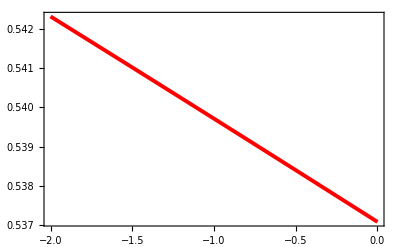

```mathematica
th=0.007;
ListPlot[{skinlist29},Frame->True,Joined->True,FrameTicks->All,PlotRange->All,PlotStyle->{{Thickness[th],Red},{Thickness[th],Blue},{Thickness[th],Green},{Thickness[th],Orange},{Thickness[th],Black}},PlotLegends->LineLegend[Automatic]]
```

```mathematica
skinlist29up={};
skinlist29down={};
Do[
j=anglesize(i-1);
AppendTo[skinlist29up,{skinlist29[[i,1]],skinlist29[[i,2]]+uncertaintylist29[[i,2]]*skinlist29[[i,2]]}];
AppendTo[skinlist29down,{skinlist29[[i,1]],skinlist29[[i,2]]-uncertaintylist29[[i,2]]*skinlist29[[i,2]]}],
{i,1,n0}]
```

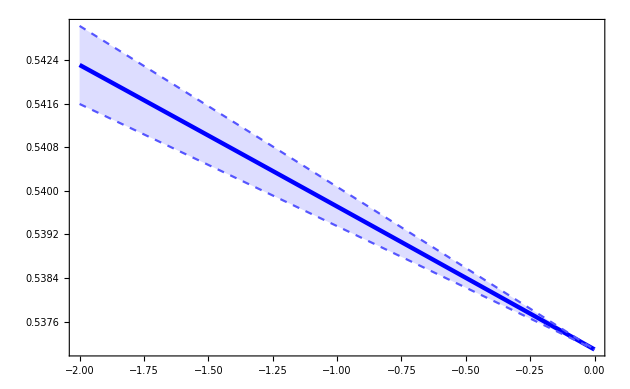

```mathematica
th=0.005;
ListLinePlot[{Sort@skinlist29,Sort@skinlist29down,Sort@skinlist29up},PlotStyle->{{Thickness[th],Blue},{Thickness[th/2],Dashed,Lighter[Blue]},{Thickness[th/2],Dashed,Lighter[Blue]}},Frame->True,FrameTicks->All,PlotRange->All,Filling->{2->{3}}]
```

Create upper ticks based on the determined linear transformation (for the second skin)

```mathematica
Rch0=2.4702;
upperTicksMajor=Module[{labels,positions},labels=Range[-0.02Rch0,0,0.005Rch0];
positions=100/Rch0#&@labels;
Transpose[{positions,labels}]];
upperTicksMinor=Module[{labels,positions,size},labels=Range[-0.02Rch0,0,0.001Rch0];
positions=100/Rch0#&/@labels;
labels=""&/@Range[Length[labels]];
Transpose[{positions,labels}]];
upperTicksMajor;
upperTicksMinor;
sizeupper:=0.012;
sizeminor:=0.006;
listUpperMajor={};listUpperMinor={};
Do[AppendTo[listUpperMajor,{upperTicksMajor[[i,1]],NumberForm[upperTicksMajor[[i,2]],3],{sizeupper,0}}],{i,1,Length[upperTicksMajor]}];
Do[AppendTo[listUpperMinor,{upperTicksMinor[[i,1]],NumberForm[upperTicksMinor[[i,2]],3],{sizeminor,0}}],{i,1,Length[upperTicksMinor]}];

listUpperMajor;
listUpperMinor;
```

```mathematica
listUpperMajor={{-2.,NumberForm[-0.0494,3],{0.012,0}},{-1.5000000000000002,NumberForm[-0.0371,3],{0.012,0}},{-1.,NumberForm[-0.0247,3],{0.012,0}},{-0.5,NumberForm[-0.0124,3],{0.012,0}},{0.0,"0.0",{0.012,0}}};
```

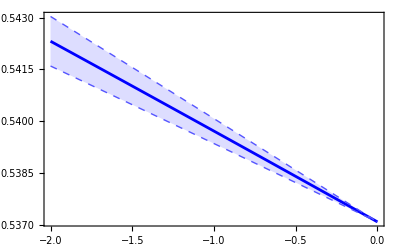

```mathematica
th=0.005;
ListLinePlot[{Sort@skinlist29,Sort@skinlist29down,Sort@skinlist29up},PlotStyle->{{Thickness[th],Blue},{Thickness[th/2],Dashed,Lighter[Blue]},{Thickness[th/2],Dashed,Lighter[Blue]}},Frame->True,Filling->{2->{3}},FrameTicks->{{All,All},{All,Join[listUpperMajor,listUpperMinor]}}]
```

```mathematica
model29=a0+a1 x;
fit29=FindFit[skinlist29,model29,{a0,a1},x];
modelf29=Function[{x},Evaluate[model29/.fit29]];
model29up=a0+a1 x;
fit29up=FindFit[skinlist29up,model29up,{a0,a1},x];
modelf29up=Function[{x},Evaluate[model29up/.fit29up]];
model29down=a0+a1 x;
fit29down=FindFit[skinlist29down,model29down,{a0,a1},x];
modelf29down=Function[{x},Evaluate[model29down/.fit29down]];
lambda0=-0.00895;
x0=100*lambda0;
A029=modelf29[x0]
AUP29=A029+0.003A029
ADOWN29=A029-0.003A029
```

0.539435

0.541053

0.537817

Forward sensitivity plot

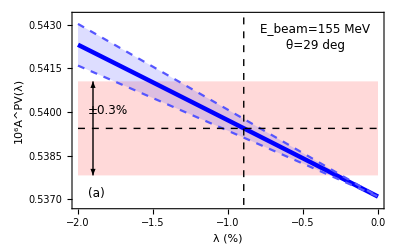

```mathematica
AT:=0.5433;
AB:=0.5368;
lambda0:=-0.895;
VertLine29:=Line[{{lambda0,AB},{lambda0,AT}}];
HorLine29:=Line[{{skinlist29[[n0,1]],A029},{skinlist29[[1,1]],A029}}];
th=0.008;
P29=ListLinePlot[{Sort@skinlist29,Sort@skinlist29down,Sort@skinlist29up},PlotRange->{{-2,0},{AB,AT}},Prolog->{{LightRed,Rectangle[{skinlist29[[n0,1]],AUP29},{skinlist29[[1,1]],ADOWN29}]}},PlotStyle->{{Thickness[th],Blue},{Thickness[th/2],Dashed,Lighter[Blue]},{Thickness[th/2],Dashed,Lighter[Blue]}},Frame->True,Filling->{2->{3}},FrameTicks->{{All,Automatic},{All,Join[listUpperMajor,listUpperMinor]}},FrameLabel->{Text[Style["λ (%)",FontSize->15]],Text[Style["10^6A^PV(λ)",FontSize->15]],Text[Style["R_wk-R_ch (fm)",FontSize->15]]},Epilog->{Text[Style["E_beam="<>ToString[Round[e1*1000]]<>" MeV",Black,FontSize->12],Scaled[{.78,.92}]],
Text[Style["θ=29 deg",Black,FontSize->12],Scaled[{.78,.83}]],Text[Style["(a)",Black,FontSize->12],Scaled[{.077,.08}]],Text[Style["±"<>ToString[NumberForm[Abs[(AUP29-ADOWN29)/(2A029)*100],2]]<>"%",FontSize->12],Scaled[{.115,.5}]],Arrowheads[{-0.02,0.02}],Arrow[{{-1.9,AUP29},{-1.9,ADOWN29}}],Directive[Dashed],VertLine29,HorLine29},FrameTicksStyle->Directive[FontSize->11]]
```

```mathematica
Export["Af-lambda.png",P29,ImageResolution->150]
Export["Af-lambda.pdf",P29]
```

Af-lambda.png

Af-lambda.pdf

Backward measurement

Determination of the experimental uncertaintly of the backward measurement of Apv based on nuclear models data

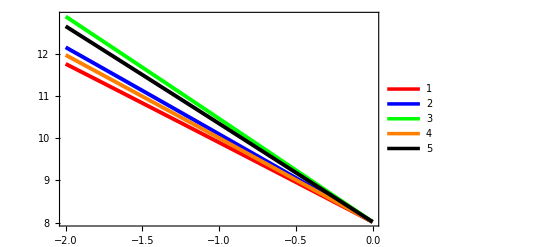

```mathematica
list={};anglelist={};
skinlist145m1={};skinlist145m2={};skinlist145m3={};skinlist145m4={};skinlist145m5={};
skinlist145m6={};
Do[
j=anglesize(i-1);
AppendTo[anglelist,data1[[i,2]]];
AppendTo[skinlist145m1,{data1[[7+j,4]]*100,10^6(data1[[7+j,3]]-data2[[7+j,3]])/(data1[[7+j,3]]+data2[[7+j,3]])}],
{i,1,n1/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist145m2,{data3[[7+j,4]]*100,10^6(data3[[7+j,3]]-data4[[7+j,3]])/(data3[[7+j,3]]+data4[[7+j,3]])}],
{i,1,n2/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist145m3,{data5[[7+j,4]]*100,10^6(data5[[7+j,3]]-data6[[7+j,3]])/(data5[[7+j,3]]+data6[[7+j,3]])}],
{i,1,n3/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist145m4,{data7[[7+j,4]]*100,10^6(data7[[7+j,3]]-data8[[7+j,3]])/(data7[[7+j,3]]+data8[[7+j,3]])}],
{i,1,n4/anglesize}]
Do[
j=anglesize(i-1);
AppendTo[skinlist145m5,{data9[[7+j,4]]*100,10^6(data9[[7+j,3]]-data10[[7+j,3]])/(data9[[7+j,3]]+data10[[7+j,3]])}],
{i,1,n5/anglesize}]


th=0.007;
ListPlot[{skinlist145m1,skinlist145m2,skinlist145m3,skinlist145m4,skinlist145m5},Frame->True,Joined->True,FrameTicks->All,PlotRange->All,PlotLegends->Automatic,PlotStyle->{{Thickness[th],Red},{Thickness[th],Blue},{Thickness[th],Green},{Thickness[th],Orange},{Thickness[th],Black},{Thickness[th],Dashed,Gray}},PlotLegends->LineLegend[Automatic]]
```

Conclusion: the largest spread is due to difference between model3 and model1

```mathematica
uncertaintylist145={};
Do[
AppendTo[uncertaintylist145,{skinlist145m3[[i,1]],(skinlist145m3[[i,2]]-skinlist145m1[[i,2]])/(skinlist145m3[[i,2]]+skinlist145m1[[i,2]])}],
{i,1,n5/anglesize}];
uncertaintylist145
```

{{0.,0.},{-0.01,0.000353993},{-0.02,0.000707447},{-0.03,0.00105605},{-0.04,0.00140437},{-0.05,0.00175255},{-0.06,0.00209627},{-0.07,0.00243796},{-0.08,0.00277841},{-0.09,0.00312001},{-0.1,0.00345441},{-0.11,0.00378845},{-0.12,0.00412454},{-0.13,0.00445697},{-0.14,0.00478723},{-0.15,0.0051157},{-0.16,0.00544196},{-0.17,0.0057669},{-0.18,0.00609161},{-0.19,0.00641114},{-0.2,0.00672941},{-0.21,0.00704984},{-0.22,0.00736584},{-0.23,0.00767952},{-0.24,0.00799248},{-0.25,0.00830627},{-0.26,0.00861343},{-0.27,0.00891947},{-0.28,0.00922739},{-0.29,0.00953129},{-0.3,0.00983628},{-0.31,0.0101361},{-0.32,0.0104369},{-0.33,0.010737},{-0.34,0.0110343},{-0.35,0.0113308},{-0.36,0.0116261},{-0.37,0.0119181},{-0.38,0.0122104},{-0.39,0.0124989},{-0.4,0.0127875},{-0.41,0.0130773},{-0.42,0.013362},{-0.43,0.0136475},{-0.44,0.0139269},{-0.45,0.0142108},{-0.46,0.0144931},{-0.47,0.014771},{-0.48,0.0150444},{-0.49,0.0153223},{-0.5,0.0155951},{-0.51,0.0158692},{-0.52,0.0161409},{-0.53,0.0164115},{-0.54,0.0166819},{-0.55,0.0169473},{-0.56,0.0172176},{-0.57,0.0174825},{-0.58,0.0177456},{-0.59,0.0180071},{-0.6,0.0182705},{-0.61,0.0185313},{-0.62,0.0187877},{-0.63,0.0190491},{-0.64,0.0193046},{-0.65,0.0195568},{-0.66,0.0198164},{-0.67,0.0200682},{-0.68,0.02032},{-0.69,0.0205681},{-0.7,0.02082},{-0.71,0.0210672},{-0.72,0.0213149},{-0.73,0.0215626},{-0.74,0.0218075},{-0.75,0.0220524},{-0.76,0.0222974},{-0.77,0.0225356},{-0.78,0.0227774},{-0.79,0.0230184},{-0.8,0.0232557},{-0.81,0.0234938},{-0.82,0.0237306},{-0.83,0.0239633},{-0.84,0.0241993},{-0.85,0.0244331},{-0.86,0.0246641},{-0.87,0.0248979},{-0.88,0.0251246},{-0.89,0.0253534},{-0.9,0.0255836},{-0.91,0.0258095},{-0.92,0.0260357},{-0.93,0.0262593},{-0.94,0.0264851},{-0.95,0.0267056},{-0.96,0.0269292},{-0.97,0.0271512},{-0.98,0.027368},{-0.99,0.0275871},{-1.,0.0278075},{-1.01,0.0280226},{-1.02,0.0282413},{-1.03,0.0284559},{-1.04,0.0286732},{-1.05,0.0288827},{-1.06,0.0290965},{-1.07,0.0293087},{-1.08,0.0295187},{-1.09,0.0297289},{-1.1,0.0299385},{-1.11,0.0301453},{-1.12,0.0303529},{-1.13,0.0305583},{-1.14,0.0307642},{-1.15,0.0309693},{-1.16,0.0311736},{-1.17,0.0313775},{-1.18,0.0315812},{-1.19,0.0317798},{-1.2,0.0319797},{-1.21,0.0321811},{-1.22,0.0323771},{-1.23,0.0325762},{-1.24,0.0327724},{-1.25,0.0329693},{-1.26,0.0331614},{-1.27,0.0333573},{-1.28,0.0335525},{-1.29,0.0337452},{-1.3,0.0339381},{-1.31,0.0341287},{-1.32,0.03432},{-1.33,0.0345104},{-1.34,0.0346985},{-1.35,0.034886},{-1.36,0.0350761},{-1.37,0.0352635},{-1.38,0.0354493},{-1.39,0.0356345},{-1.4,0.0358197},{-1.41,0.0360023},{-1.42,0.0361853},{-1.43,0.0363684},{-1.44,0.0365489},{-1.45,0.0367286},{-1.46,0.0369118},{-1.47,0.0370923},{-1.48,0.0372697},{-1.49,0.0374486},{-1.5,0.0376241},{-1.51,0.0378007},{-1.52,0.0379767},{-1.53,0.0381538},{-1.54,0.0383278},{-1.55,0.0385011},{-1.56,0.0386761},{-1.57,0.0388491},{-1.58,0.0390214},{-1.59,0.0391929},{-1.6,0.0393623},{-1.61,0.0395328},{-1.62,0.039702},{-1.63,0.039872},{-1.64,0.0400389},{-1.65,0.0402068},{-1.66,0.0403727},{-1.67,0.0405391},{-1.68,0.0407046},{-1.69,0.0408694},{-1.7,0.0410346},{-1.71,0.0411981},{-1.72,0.0413612},{-1.73,0.0415251},{-1.74,0.0416848},{-1.75,0.0418471},{-1.76,0.0420063},{-1.77,0.0421654},{-1.78,0.042327},{-1.79,0.0424853},{-1.8,0.0426433},{-1.81,0.0428005},{-1.82,0.0429579},{-1.83,0.0431144},{-1.84,0.0432721},{-1.85,0.0434268},{-1.86,0.0435805},{-1.87,0.0437367},{-1.88,0.0438882},{-1.89,0.0440428},{-1.9,0.0441944},{-1.91,0.0443481},{-1.92,0.0444999},{-1.93,0.0446488},{-1.94,0.0448008},{-1.95,0.0449499},{-1.96,0.0450975},{-1.97,0.0452465},{-1.98,0.0453958},{-1.99,0.0455441},{-2.,0.0456916}}

Read off Coulomb distorted data with our parametrisation of the weak density

```mathematica
n0=201;
skinlist145={};anglelist={};
Do[
j=anglesize(i-1);
AppendTo[skinlist145,{skinlist145m1[[i,1]],skinlist145m1[[i,2]]+(skinlist145m3[[i,2]]-skinlist145m1[[i,2]])/2}],
{i,1,n0}]
```

```mathematica
skinlist145
```

{{0.,8.01557},{-0.01,8.03736},{-0.02,8.05919},{-0.03,8.08101},{-0.04,8.10281},{-0.05,8.12466},{-0.06,8.14647},{-0.07,8.16828},{-0.08,8.1901},{-0.09,8.21189},{-0.1,8.2337},{-0.11,8.25551},{-0.12,8.27729},{-0.13,8.2991},{-0.14,8.32088},{-0.15,8.34267},{-0.16,8.36448},{-0.17,8.38626},{-0.18,8.40805},{-0.19,8.42983},{-0.2,8.45162},{-0.21,8.47341},{-0.22,8.49517},{-0.23,8.51695},{-0.24,8.53873},{-0.25,8.56053},{-0.26,8.58226},{-0.27,8.60404},{-0.28,8.62579},{-0.29,8.64756},{-0.3,8.66933},{-0.31,8.69111},{-0.32,8.7128},{-0.33,8.73458},{-0.34,8.75636},{-0.35,8.77809},{-0.36,8.79983},{-0.37,8.8216},{-0.38,8.84333},{-0.39,8.8651},{-0.4,8.88683},{-0.41,8.90857},{-0.42,8.93031},{-0.43,8.952},{-0.44,8.97376},{-0.45,8.99548},{-0.46,9.01721},{-0.47,9.03893},{-0.48,9.06067},{-0.49,9.08236},{-0.5,9.1041},{-0.51,9.12581},{-0.52,9.1475},{-0.53,9.16924},{-0.54,9.19098},{-0.55,9.21263},{-0.56,9.23438},{-0.57,9.25608},{-0.58,9.27775},{-0.59,9.29946},{-0.6,9.32117},{-0.61,9.34286},{-0.62,9.36455},{-0.63,9.38625},{-0.64,9.40791},{-0.65,9.42961},{-0.66,9.45132},{-0.67,9.47294},{-0.68,9.49464},{-0.69,9.51634},{-0.7,9.53801},{-0.71,9.55967},{-0.72,9.58136},{-0.73,9.603},{-0.74,9.62467},{-0.75,9.64632},{-0.76,9.66802},{-0.77,9.68966},{-0.78,9.71132},{-0.79,9.73298},{-0.8,9.75463},{-0.81,9.77625},{-0.82,9.79791},{-0.83,9.81959},{-0.84,9.84119},{-0.85,9.86284},{-0.86,9.88447},{-0.87,9.90611},{-0.88,9.92776},{-0.89,9.9494},{-0.9,9.97102},{-0.91,9.99265},{-0.92,10.0143},{-0.93,10.0359},{-0.94,10.0576},{-0.95,10.0791},{-0.96,10.1008},{-0.97,10.1224},{-0.98,10.144},{-0.99,10.1656},{-1.,10.1872},{-1.01,10.2088},{-1.02,10.2304},{-1.03,10.252},{-1.04,10.2736},{-1.05,10.2952},{-1.06,10.3168},{-1.07,10.3384},{-1.08,10.36},{-1.09,10.3816},{-1.1,10.4032},{-1.11,10.4248},{-1.12,10.4463},{-1.13,10.4679},{-1.14,10.4895},{-1.15,10.5111},{-1.16,10.5326},{-1.17,10.5542},{-1.18,10.5758},{-1.19,10.5973},{-1.2,10.6189},{-1.21,10.6405},{-1.22,10.662},{-1.23,10.6836},{-1.24,10.7051},{-1.25,10.7267},{-1.26,10.7483},{-1.27,10.7698},{-1.28,10.7913},{-1.29,10.8129},{-1.3,10.8344},{-1.31,10.856},{-1.32,10.8775},{-1.33,10.899},{-1.34,10.9206},{-1.35,10.9421},{-1.36,10.9636},{-1.37,10.9852},{-1.38,11.0067},{-1.39,11.0282},{-1.4,11.0497},{-1.41,11.0713},{-1.42,11.0928},{-1.43,11.1143},{-1.44,11.1358},{-1.45,11.1573},{-1.46,11.1788},{-1.47,11.2004},{-1.48,11.2219},{-1.49,11.2433},{-1.5,11.2649},{-1.51,11.2864},{-1.52,11.3078},{-1.53,11.3293},{-1.54,11.3508},{-1.55,11.3723},{-1.56,11.3938},{-1.57,11.4153},{-1.58,11.4368},{-1.59,11.4582},{-1.6,11.4797},{-1.61,11.5012},{-1.62,11.5227},{-1.63,11.5441},{-1.64,11.5656},{-1.65,11.5871},{-1.66,11.6085},{-1.67,11.63},{-1.68,11.6514},{-1.69,11.6729},{-1.7,11.6944},{-1.71,11.7158},{-1.72,11.7373},{-1.73,11.7587},{-1.74,11.7802},{-1.75,11.8016},{-1.76,11.8231},{-1.77,11.8445},{-1.78,11.866},{-1.79,11.8874},{-1.8,11.9088},{-1.81,11.9302},{-1.82,11.9517},{-1.83,11.9731},{-1.84,11.9945},{-1.85,12.0159},{-1.86,12.0373},{-1.87,12.0588},{-1.88,12.0802},{-1.89,12.1016},{-1.9,12.123},{-1.91,12.1444},{-1.92,12.1658},{-1.93,12.1873},{-1.94,12.2087},{-1.95,12.23},{-1.96,12.2514},{-1.97,12.2728},{-1.98,12.2942},{-1.99,12.3156},{-2.,12.337}}

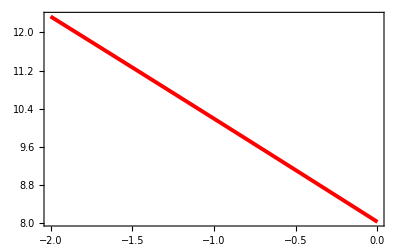

```mathematica
th=0.007;
ListPlot[{skinlist145},Frame->True,Joined->True,FrameTicks->All,PlotRange->All,PlotStyle->{{Thickness[th],Red},{Thickness[th],Blue},{Thickness[th],Green},{Thickness[th],Orange},{Thickness[th],Black}},PlotLegends->LineLegend[Automatic]]
```

```mathematica
skinlist145up={};
skinlist145down={};
Do[
j=anglesize(i-1);
AppendTo[skinlist145up,{skinlist145[[i,1]],skinlist145[[i,2]]+uncertaintylist145[[i,2]]*skinlist145[[i,2]]}];
AppendTo[skinlist145down,{skinlist145[[i,1]],skinlist145[[i,2]]-uncertaintylist145[[i,2]]*skinlist145[[i,2]]}],
{i,1,n0}]
```

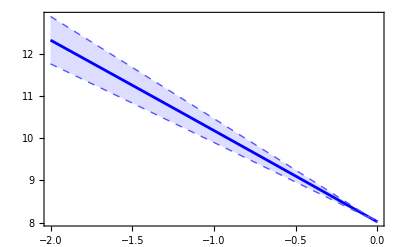

```mathematica
th=0.005;
ListLinePlot[{Sort@skinlist145,Sort@skinlist145down,Sort@skinlist145up},PlotStyle->{{Thickness[th],Blue},{Thickness[th/2],Dashed,Lighter[Blue]},{Thickness[th/2],Dashed,Lighter[Blue]}},Frame->True,FrameTicks->All,PlotRange->All,Filling->{2->{3}}]
```

Fit of 145 degrees data

```mathematica
model145=a0+a1 x;
fit145=FindFit[skinlist145,model145,{a0,a1},x];
modelf145=Function[{x},Evaluate[model145/.fit145]];
model145up=a0+a1 x;
fit145up=FindFit[skinlist145up,model145up,{a0,a1,a2},x];
modelf145up=Function[{x},Evaluate[model145up/.fit145up]];
model145down=a0+a1 x;
fit145down=FindFit[skinlist145down,model145down,{a0,a1,a2},x];
modelf145down=Function[{x},Evaluate[model145down/.fit145down]];
lambda0=-0.895;
x0=lambda0;
A0145=modelf145[x0]
AUP145=A0145+0.07A0145
ADOWN145=A0145-0.07A0145
```

9.95665

10.6536

9.25968

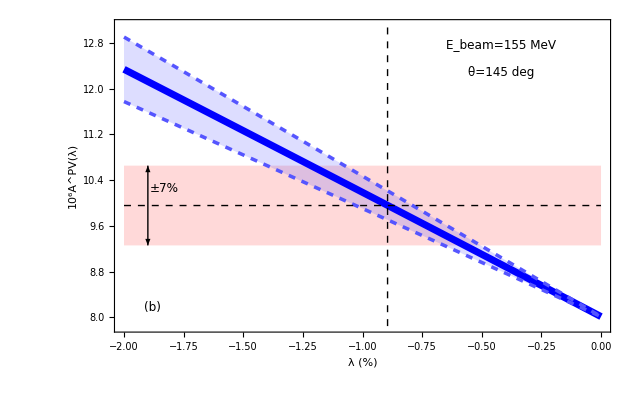

```mathematica
AT=13.1;
AB=7.85;
VertLine145=Line[{{lambda0,AB},{lambda0,AT}}];
HorLine145=Line[{{skinlist145[[n0,1]],A0145},{skinlist145[[1,1]],A0145}}];
th=0.008;
P145=ListLinePlot[{Sort@skinlist145,Sort@skinlist145down,Sort@skinlist145up},PlotRange->{{-2,skinlist145[[1,1]]},{AB,AT}},Prolog->{{LightRed,Rectangle[{skinlist145[[n0,1]],AUP145},{skinlist29[[1,1]],ADOWN145}]}},PlotStyle->{{Thickness[th],Blue},{Thickness[th/2],Dashed,Lighter[Blue]},{Thickness[th/2],Dashed,Lighter[Blue]}},Frame->True,Filling->{2->{3}},FrameTicks->{{All,Automatic},{All,Join[listUpperMajor,listUpperMinor]}},FrameLabel->{Text[Style["λ (%)",FontSize->15]],Text[Style["10^6A^PV(λ)",FontSize->15]],Text[Style["R_wk-R_ch (fm)",FontSize->15]]},Epilog->{Text[Style["E_beam="<>ToString[Round[e1*1000]]<>" MeV",Black,FontSize->12],Scaled[{.78,.92}]],
Text[Style["θ=145 deg",Black,FontSize->12],Scaled[{.78,.83}]],Text[Style["(b)",Black,FontSize->12],Scaled[{.077,.08}]],Text[Style["±"<>ToString[IntegerPart[Round[Abs[(AUP145-ADOWN145)/(2A0145)*100]]]]<>"%",FontSize->12],Scaled[{.10,.46}]],Arrowheads[{-0.02,0.02}],Arrow[{{-1.9,AUP145},{-1.9,ADOWN145}}],Directive[Dashed],VertLine145,HorLine145},FrameTicksStyle->Directive[FontSize->11]]
```

```mathematica
(modelf145[-2]-A0145)/A0145
(A0145-modelf145[0])/modelf145[0]
```

0.239801

0.241046

```mathematica
Export["Ab-lambda.png",P145,ImageResolution->150]
Export["Ab-lambda.pdf",P145]
```

Ab-lambda.png

Ab-lambda.pdf

Chi2

```mathematica
AfExp=modelf29[x0]
AbExp=modelf145[x0]
dAf=0.003AfExp;
dAb1=0.03AbExp;
dAb2=0.07AbExp;
dAb3=0.1AbExp;
dp=1;
p0:=0;
lambda0=-0.895;
```

0.539435

9.95665

```mathematica
a0f=modelf29[x0]/s2w
a0b=modelf145[x0]/s2w
df=1/lambda0(1-modelf29[0]/(a0f s2w))
db=1/lambda0(1-modelf145[0]/(a0b s2w))
bf=1/lambda0(modelf29up[x0]/(a0f s2w)-1)
bb=1/lambda0(modelf145up[x0]/(a0b s2w)-1)
```

2.26008

41.7155

-0.00484523

-0.217015

-0.000667185

-0.0284135

```mathematica
pb0f=-df*lambda0
pb0b=-db*lambda0
pb1f=df
pb1b=db
pb2f=bf
pb2b=bb
```

-0.00433648

-0.194228

-0.00484523

-0.217015

-0.000667185

-0.0284135

```mathematica
Ai[q_]:= (24Gf q^2)/(4Sqrt[2]Pi alpha)1/Z*10^6
```

```mathematica
p0f=a0f/Ai[q1]-1+a0f/Ai[q1] pb0f
p0b=a0b/Ai[q2]-1+a0b/Ai[q2] pb0b
p1f=a0f/Ai[q1] pb1f
p1b=a0b/Ai[q2] pb1b
p2f=a0f/Ai[q1] pb2f
p2b=a0b/Ai[q2] pb2b
```

0.0400591

0.0958644

-0.00506127

-0.295144

-0.000696934

-0.0386429

```mathematica
Af[sw_,lambda_,p_]:=a0f sw(1+(df+bf p)lambda-df lambda0)
Ab[sw_,lambda_,p_]:=a0b sw(1+(db+bb p)lambda-db lambda0)
```

```mathematica
chi2[sw_,lambda_,p_,dAb_]:=((AfExp-Af[sw,lambda,p])/dAf)^2+((AbExp-Ab[sw,lambda,p])/dAb)^2+((p-p0)/dp)^2
chi0=1;
```

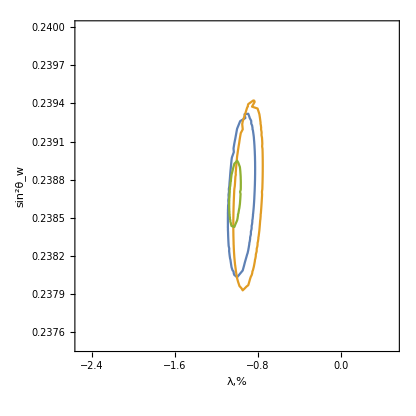

```mathematica
ContourPlot[{chi2[x,y,-0.5,dAb1]==chi0,chi2[x,y,0,dAb1]==chi0,chi2[x,y,-0.936,dAb1]==chi0},{y,0.5,-2.5},{x,0.2375,0.24},FrameLabel->{"λ,%","sin^2θ_w"}]
```

Create upper ticks for ellipses

```mathematica
Rch0=2.4702;
upperTicksMajor=Module[{labels,positions},labels=Range[-0.02Rch0,0.010Rch0,0.005Rch0];
positions=100/Rch0#&@labels;
Transpose[{positions,labels}]];
upperTicksMinor=Module[{labels,positions,size},labels=Range[-0.03Rch0,0.0250Rch0,0.001Rch0];
positions=100/Rch0#&/@labels;
labels=""&/@Range[Length[labels]];
Transpose[{positions,labels}]];
upperTicksMajor;
upperTicksMinor;
sizeupper:=0.012;
sizeminor:=0.006;
listUpperMajor={};listUpperMinor={};
Do[AppendTo[listUpperMajor,{upperTicksMajor[[i,1]],NumberForm[upperTicksMajor[[i,2]],3],{sizeupper,0}}],{i,1,Length[upperTicksMajor]}];
Do[AppendTo[listUpperMinor,{upperTicksMinor[[i,1]],NumberForm[upperTicksMinor[[i,2]],3],{sizeminor,0}}],{i,1,Length[upperTicksMinor]}];

listUpperMajor;
listUpperMinor;
```

```mathematica
listUpperMajor={{-2.,NumberForm[-0.0494,3],{0.012,0}},{-1.5000000000000002,NumberForm[-0.0371,3],{0.012,0}},{-1.,NumberForm[-0.0247,3],{0.012,0}},{-0.5,NumberForm[-0.0124,3],{0.012,0}},{0.0,"0.0",{0.012,0}}};
```

Results

```mathematica
cp1=ContourPlot3D[{chi2[x,y,z,dAb1]==chi0},{y,-0.1,-2.3},{x,0.237,0.2404},{z,-dp,dp},BoundaryStyle->Directive[Red, Thick],Mesh->None,PlotRange->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot[chi2[x,y,z,dAb1]==chi0,{y,-1.097,-0.724},{x,0.23792,0.23943},FrameLabel->{"λ, %","sin^2θ_w"}],{z,-dp,dp,Appearance->"Labeled"}]
```

```mathematica
R1=ImplicitRegion[chi2[x,y,z,dAb1]<=chi0,{{x,-∞,∞},{y,-∞,∞},{z,-dp,dp}}];
```

```mathematica
xi1=-1.8;xf1=0.3;yi1=0.2373;yf1=0.2400;
el1=-1.097;er1=-0.724;eb1=0.23792;et1=0.23943;
```

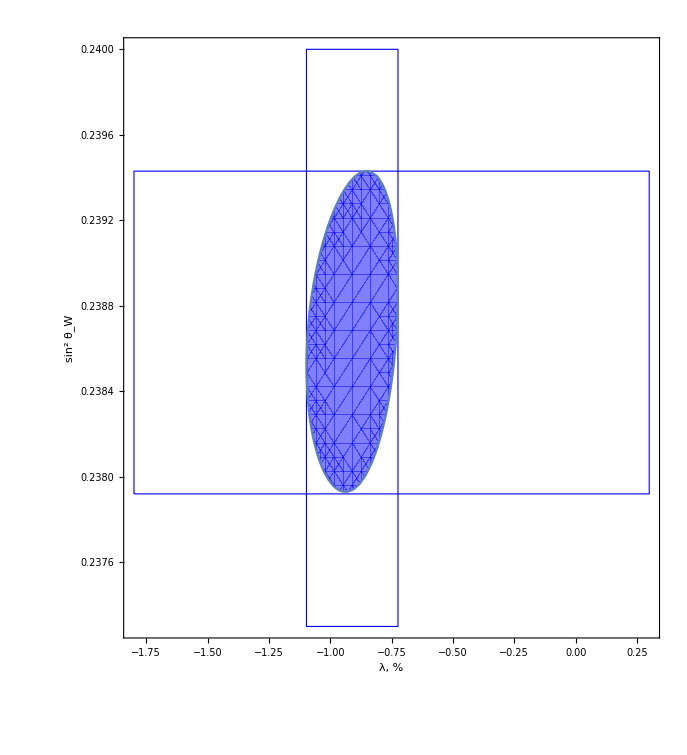

```mathematica
g1=RegionPlot[Resolve[Exists[z,{x,y,z}∈R1],Reals],{y,-1.5,-0.1},{x,0.2375,0.2400},Frame->True,AspectRatio->1.1/1,PlotStyle->{Blue,Opacity[0.5]},FrameLabel->{Text[Style["λ, %",FontSize->15]],Text[Style["sin^2 θ_W",FontSize->15]],Text[Style["R_wk-R_ch, fm",FontSize->15]]},PlotRange->{{xi1,xf1},{yi1,yf1}},FrameTicks->{{All,Automatic},{All,Join[listUpperMajor,listUpperMinor]}},FrameStyle->Directive[11],Prolog->{{EdgeForm[{Dashed,Blue}],FaceForm[],Rectangle[{el1,yi1},{er1,yf1}]},{EdgeForm[{Dashed,Blue}],FaceForm[],Rectangle[{xi1,eb1},{xf1,et1}]}}]
```

```mathematica
cp2=ContourPlot3D[{chi2[x,y,z,dAb2]==chi0},{y,0.3,-2.8},{x,0.236,0.241},{z,-dp,dp},BoundaryStyle->Directive[Red, Thick],Mesh->None,PlotRange->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot[chi2[x,y,z,dAb2]==chi0,{y,-1.265,-0.557},{x,0.23785,0.23951},FrameLabel->{"λ, %","sin^2θ_w"}],{z,-dp,dp,Appearance->"Labeled"}]
```

```mathematica
R2=ImplicitRegion[chi2[x,y,z,dAb2]<=chi0,{{x,-∞,∞},{y,-∞,∞},{z,-dp,dp}}];
```

```mathematica
xi2=-1.8;xf2=0.3;yi2=0.2373;yf2=0.2400;
el2=-1.265;er2=-0.557;eb2=0.23785;et2=0.23951;
```

```mathematica
(et1-eb1)/2/s2w
(er1-el1)/2
```

0.00316323

0.1865

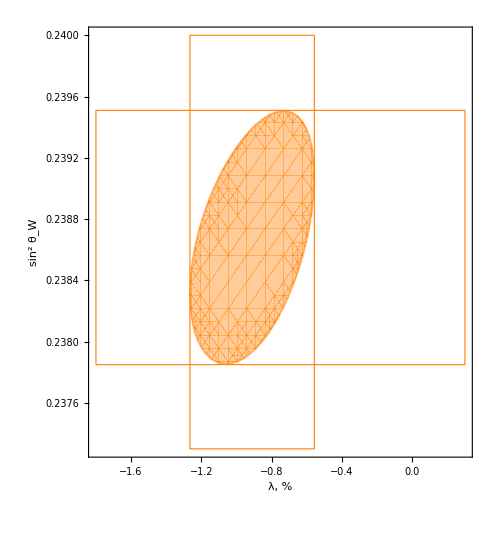

```mathematica
g2=RegionPlot[Resolve[Exists[z,{x,y,z}∈R2],Reals],{y,-2.1,-0.1},{x,0.237,0.2403},Frame->True,AspectRatio->1.1/1,PlotStyle->{Orange,Opacity[0.4]},BoundaryStyle->{Orange,Opacity[0.4]},FrameLabel->{Text[Style["λ, %",FontSize->17]],Text[Style["sin^2 θ_W",FontSize->17]],Text[Style["R_wk-R_ch, fm",FontSize->17]]},PlotRange->{{xi2,xf2},{yi2,yf2}},FrameTicks->{{All,Automatic},{All,Join[listUpperMajor,listUpperMinor]}},FrameStyle->Directive[13],Prolog->{{EdgeForm[{Dashed,Orange}],FaceForm[],Rectangle[{el2,yi2},{er2,yf2}]},{EdgeForm[{Dashed,Orange}],FaceForm[],Rectangle[{xi2,eb2},{xf2,et2}]}}]
```

```mathematica
cp3=ContourPlot3D[{chi2[x,y,z,dAb3]==chi0},{y,1.5,-3.8},{x,0.236,0.242},{z,-dp,dp},BoundaryStyle->Directive[Red, Thick],Mesh->None]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot[chi2[x,y,z,dAb3]==chi0,{y,-1.402,-0.421},{x,0.23776,0.23960},FrameLabel->{"λ, %","sin^2θ_w"}],{z,-dp,dp,Appearance->"Labeled"}]
```

```mathematica
R3=ImplicitRegion[chi2[x,y,z,dAb3]<=chi0,{{x,-∞,∞},{y,-∞,∞},{z,-dp,dp}}];
```

```mathematica
xi3=-1.8;xf3=0.3;yi3=0.2373;yf3=0.2400;
el3=-1.402;er3=-0.421;eb3=0.23776;et3=0.23960;
```

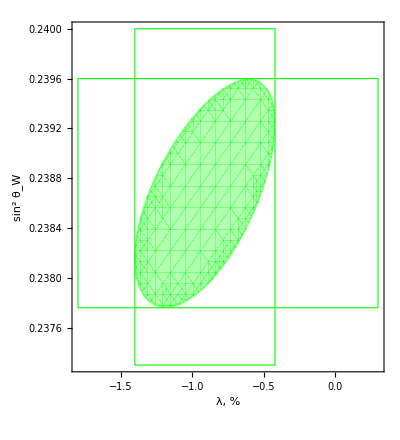

```mathematica
g3=RegionPlot[Resolve[Exists[z,{x,y,z}∈R3],Reals],{y,-2.1,-0.1},{x,0.237,0.2403},Frame->True,AspectRatio->1.1/1,PlotStyle->{Green,Opacity[0.3]},BoundaryStyle->{Green,Opacity[0.3]},FrameLabel->{Text[Style["λ, %",FontSize->17]],Text[Style["sin^2 θ_W",FontSize->17]],Text[Style["R_wk-R_ch, fm",FontSize->17]]},PlotRange->{{xi3,xf3},{yi3,yf3}},FrameTicks->{{All,Automatic},{All,Join[listUpperMajor,listUpperMinor]}},FrameStyle->Directive[13],Prolog->{{EdgeForm[{Dashed,Green}],FaceForm[],Rectangle[{el3,yi3},{er3,yf3}]},{EdgeForm[{Dashed,Green}],FaceForm[],Rectangle[{xi3,eb3},{xf3,et3}]}}]
```

```mathematica
g1=RegionPlot[Resolve[Exists[z,{x,y,z}∈R1],Reals],{y,-2.1,-0.1},{x,0.237,0.2403},Frame->True,AspectRatio->1.1/1,PlotStyle->{Lighter[Blue,0.4]},BoundaryStyle->{Lighter[Blue]},PlotRange->{{xi1,xf1},{yi1,yf1}}];
g2=RegionPlot[Resolve[Exists[z,{x,y,z}∈R2],Reals],{y,-2.1,-0.1},{x,0.237,0.2403},Frame->True,AspectRatio->1.1/1,PlotStyle->{Lighter[Orange,0.4]},BoundaryStyle->{Lighter[Orange]},PlotRange->{{xi2,xf2},{yi2,yf2}}];
g3=RegionPlot[Resolve[Exists[z,{x,y,z}∈R3],Reals],{y,-2.1,-0.1},{x,0.237,0.2403},Frame->True,FrameLabel->{Text[Style["λ (%)",FontSize->15]],Text[Style["sin^2 θ_W",FontSize->15]],Text[Style["R_wk-R_ch (fm)",FontSize->15]]},AspectRatio->1.1/1,PlotStyle->{Lighter[Green,0.4]},BoundaryStyle->{Lighter[Green]},PlotRange->{{xi3,xf3},{yi3,yf3}},FrameTicks->{{All,Automatic},{All,Join[listUpperMajor,listUpperMinor]}},FrameStyle->Directive[11]];
```

```mathematica
HorLine1t=Line[{{xi1,et1},{xf1,et1}}];
HorLine1b=Line[{{xi1,eb1},{xf1,eb1}}];
HorLine2t=Line[{{xi2,et2},{xf2,et2}}];
HorLine2b=Line[{{xi2,eb2},{xf2,eb2}}];
HorLine3t=Line[{{xi3,et3},{xf3,et3}}];
HorLine3b=Line[{{xi3,eb3},{xf3,eb3}}];
VertLine1l=Line[{{el1,yi1},{el1,yf1}}];
VertLine1r=Line[{{er1,yi1},{er1,yf1}}];
VertLine2l=Line[{{el2,yi2},{el2,yf2}}];
VertLine2r=Line[{{er2,yi2},{er2,yf2}}];
VertLine3l=Line[{{el3,yi3},{el3,yf3}}];
VertLine3r=Line[{{er3,yi3},{er3,yf3}}];
```

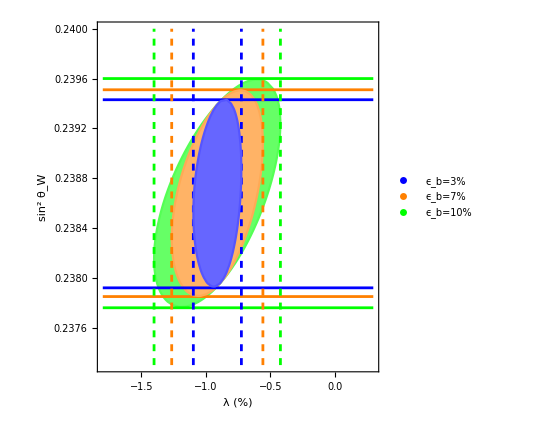

```mathematica
th1=0.005;
th2=0.005;
EL=Legended[Show[g3,g2,g1,Epilog->{Directive[Blue,Thickness[th1]],HorLine1t,HorLine1b,Directive[Orange,Thickness[th1]],HorLine2t,HorLine2b,Directive[Green,Thickness[th1]],HorLine3t,HorLine3b,Directive[Blue,Dashed,Thickness[th2]],VertLine1l,VertLine1r,Directive[Orange,Dashed,Thickness[th2]],VertLine2l,VertLine2r,Directive[Green,Dashed,Thickness[th2]],VertLine3l,VertLine3r}],Placed[PointLegend[{Blue,Orange,Green},{Text[Style["ϵ_b=3%",FontSize->15]],Text[Style["ϵ_b=7%",FontSize->15]],Text[Style["ϵ_b=10%",FontSize->15]]}],{0.855,0.5}]]
```

```mathematica
Export["X2eq1-sw2-lambda.png",EL,ImageResolution->100]
Export["X2eq1-sw2-lambda.pdf",EL]
Export["X2eq1-sw2-lambda.eps",EL]
```

X2eq1-sw2-lambda.png

X2eq1-sw2-lambda.pdf

X2eq1-sw2-lambda.eps